# Female Satisfaction - Male Muscularity

https://twitter.com/datepsych/status/1741677937038913931 
The question is, how high is the sample count? This notebook is unfair BECAUSE I am assuming based on the sparseness of the dots, I assume each dot is one sample even though this is unlikely.
Also p-values seem to be totally useless. You run a Monte Carlo simulation, you can get any p-value you want!

-Graphics-

-Graphics-

Use the coefficients.  
What does /. mean?
It means replace values.

Note that Wolfram Engine is stringent to *

Claim is made for coefficient to be robustly is zero.

```mathematica
?/.
```

Replicate the table, how is the table replicated?

```mathematica
X=Table[i,{i,1,7,1}]
```

{1,2,3,4,5,6,7}

We do not have the total sample count. In reality, I suspect only 32 surveys were done. Time to multiply the sample count by 100.

```mathematica
Y={200,200,500, 800, 900, 400, 200}
```

{200,200,500,800,900,400,200}

```mathematica
ta=Table[Table[X[[i]],{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

Makes the distribution into an empirical distribution. I doubt that there are actually 32 points.

```mathematica
dist=EmpiricalDistribution[ta]
```

DataDistribution[…]

From a power law discussion, the square of a variable has half the tail exponent.

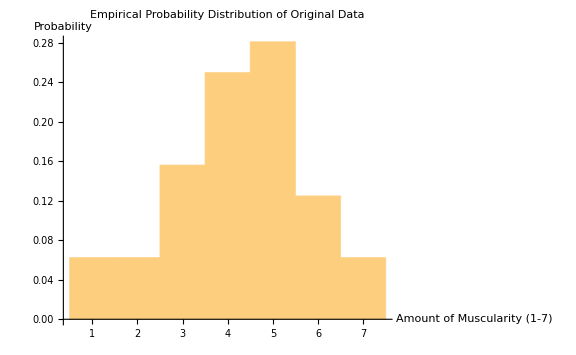

```mathematica
Histogram[ta,10,Probability,PlotLabel->"Empirical Probability Distribution of Original Data",AxesLabel->{"Amount of Muscularity (1-7)","Probability"},ImageSize->Large]
```

This is the key step in replicating the paper. Take the smooth kernel distribution. It makes the distribution of the bins smoother.

```mathematica
dist2=SmoothKernelDistribution[ta];
```

Apply N to all these values which makes them real and not fractions.

```mathematica
{Mean[dist2],Kurtosis[dist2],Skewness[dist2]}//N
```

{4.25,2.77691,-0.272711}

```mathematica
{Skewness[ta],Skewness[dist2]}//N
```

{-0.319444,-0.272711}

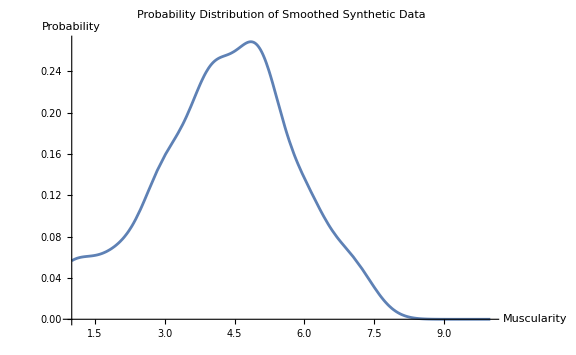

```mathematica
Plot[PDF[dist2,x],{x,1,10},PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity","Probability"},ImageSize->Large]
```

Muscularity of individuals apparently follow a normal distribution

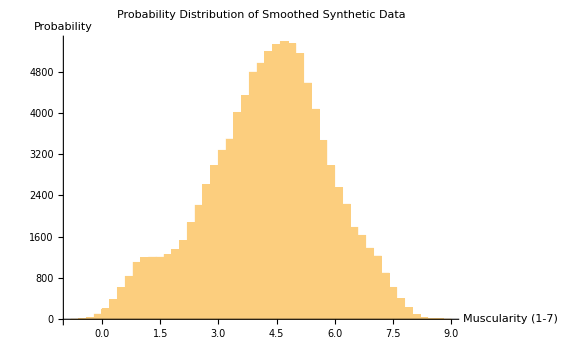

```mathematica
Histogram[RandomVariate[dist2,10^5],50,PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity (1-7)","Probability"},ImageSize->Large]
```

### Testing with No Noise

We find the gradient of a line.

```mathematica
(37-30)/7
```

1

From the picture of the graph, we derive this linear fit.

```mathematica
f=a*x+b/.{a->1,b->30};
```

Apply the regression line to the original function.

```mathematica
f1=f/.x->ta;
```

```mathematica
reg=Transpose[{ta,f1}];
```

```mathematica
lm=LinearModelFit[reg,{1,x},x];
```

Recall the table above was to get this linear regression fit of R^2=1 given the coefficients.

```mathematica
lm
```

FittedModel[30.+1. x]

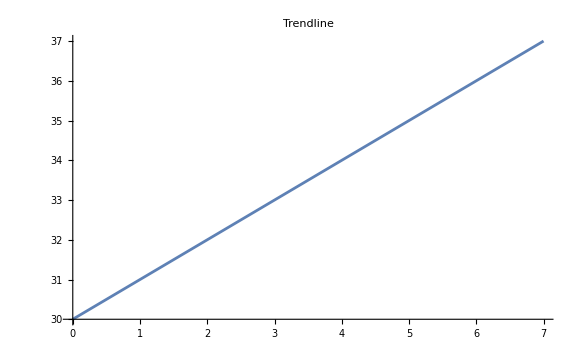

```mathematica
Plot[lm[x],{x,0,7},PlotLabel->"Trendline",ImageSize->Large]
```

Obtain the length of f1 based on the length of samples in ta.

```mathematica
f1//Length
```

3200

Apply some Gaussian noise to the function. Then perform the transpose to make it suitable for regression again.

```mathematica
reg1[sigma_]:=Transpose[{ta,f1+RandomVariate[NormalDistribution[0,sigma],Length[f1]]}]
```

Then, apply a linear model fit with the model. Check the p-value as usual, run about the model 10^4 times so as to get a distribution of possible p-values. This is the Monte Carlo simulation for possible p-value given a particular noise and eats up a lot of time. I have calibrate the noise so as to get the supposed p-value. Note that the noise to get the p-value is ridiculously high.

```mathematica
res=Table[lm=LinearModelFit[reg1[23.5],{1,x},x];lm["ParameterPValues"][[2]],{z,1,10^3}];
```

Get the assumed p-value distribution and parameters. The p-value is way too high.

```mathematica
{Mean[res],StandardDeviation[res],Skewness[res],Kurtosis[res]}
```

{0.0102108,0.0405471,7.45024,68.1675}

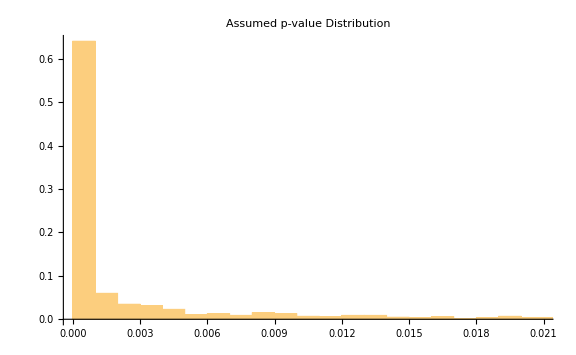

```mathematica
pl0=Histogram[res,Automatic,"Probability",PlotLabel->"Assumed p-value Distribution",ImageSize->Large]
```

Replicate the graph. From the empirical distribution. Note that I am being generous by assuming they had 3200 samples. Note that this is absolutely ridiculous, so the sample size is clearly must less than 3200. Note that to achieve this p-value, you basically have to far exceed the scale of the study in the first place as part of the empirical distribution.

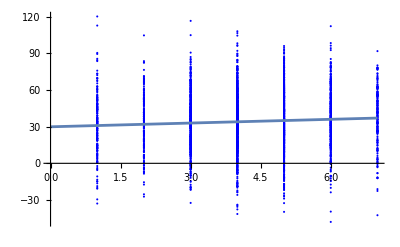

```mathematica
Show[ListPlot[reg1[23.5],PlotStyle->Blue],Plot[lm[x],{x,0,7}]]
```

### Replicating Their Linear Term

Apply the same technique, tabulate the values of the second coefficient, run the Monte Carlo simulation 10^4 times. We use purely the linear term.

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[23.5],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

Get the distribution parameters of the quadratic term.

```mathematica
{Mean[ta2],StandardDeviation[ta2],Skewness[ta2],Kurtosis[ta2]}
```

{0.998994,0.268244,-0.0340243,3.11937}

Plot the histogram of the assumed quadratic coefficient.

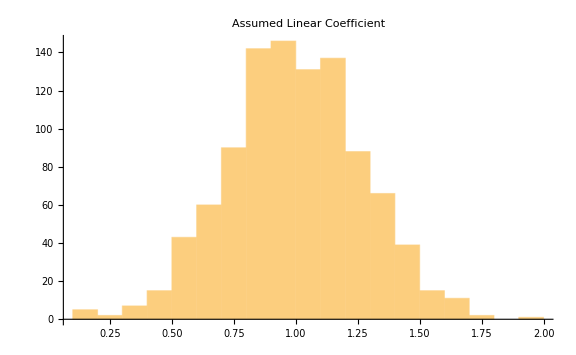

```mathematica
pl1=Histogram[ta2,PlotLabel->"Assumed Linear Coefficient",ImageSize->Large]
```

### Monte-Carlo of both the distribution and the quadratic term.

This is where you get caught out. If you have a low sample count, you should get basically nothing or no correlation. How is it possible that with such a low sample count they got such a distribution?

```mathematica
ta=RandomVariate[dist2,Length[f1]]
```

{4.9733,2.92087,6.30134,4.16208,4.96258,6.13264,4.56403,3.44536,3.84617,5.13969,4.76155,0.856265,3.04252,0.839967,4.46145,8.11522,4.45928,3.52826,2.56213,3.73232,4.89599,6.12388,4.27302,0.501658,3.77279,4.18043,5.35004,3.84573,5.45981,6.08798,1.21229,4.66077,2.92134,7.53873,3.26488,4.138,4.89758,3.38686,5.22586,5.51931,4.11199,5.74469,5.66859,4.19171,3.79067,2.02326,5.06919,3.29081,5.71631,1.79942,3.52531,4.93735,3.17106,4.72291,3.01864,5.21844,3.68813,4.97029,6.41765,5.27704,1.53258,6.19428,6.55355,3.16576,2.57765,4.13434,6.67023,4.31631,2.99904,4.32678,2.06938,4.91067,1.45389,2.71998,8.05811,4.07455,4.60504,5.19662,4.51266,4.44929,2.68203,6.2153,2.03367,6.48009,3.93386,7.10804,3.71111,4.19483,1.91438,4.15217,5.369,6.63425,4.43139,3.30077,6.81697,4.22252,4.14238,3.50144,5.49619,3.88985,1.61438,3.58963,4.70872,4.68483,5.67837,5.31575,5.25767,4.24368,2.75959,1.46895,5.41343,6.89074,3.68821,4.59978,3.63365,5.00567,5.81669,3.94262,3.53745,7.50469,3.70359,0.623696,3.44874,3.03666,5.71574,6.5021,5.81257,6.84632,5.11955,4.91947,6.10322,6.16065,3.18814,6.89903,6.84863,3.17726,1.2453,4.59547,5.33725,1.83871,5.48355,3.14333,6.48092,3.07537,4.51837,6.10579,6.54169,5.71043,2.8805,1.81872,3.4393,5.82653,0.786694,3.58577,6.47726,3.30191,1.80031,5.66168,6.41167,3.44618,6.4126,5.07418,5.51266,3.66618,4.13492,3.03946,2.99056,5.53498,5.09802,6.76457,4.22439,3.22538,4.07679,2.45524,3.45253,4.59237,6.29223,4.95001,5.59796,4.49865,4.37961,4.36307,5.92197,4.20134,2.8127,5.31492,7.0557,5.27627,4.21737,5.03636,3.60668,4.35117,3.71192,4.09587,5.38589,2.29801,6.63419,5.95364,1.98597,4.24857,2.23849,6.399,4.45375,5.31106,3.46725,4.49785,2.91288,2.80273,3.8046,0.75306,4.34282,5.6545,5.95979,5.51044,2.88443,3.48511,3.83543,0.446042,5.67776,2.56706,5.83531,3.68419,3.70946,5.4042,2.11385,4.30014,4.70289,4.852,6.93826,4.13775,4.89987,2.58726,5.69304,3.19818,3.58715,5.47744,4.72565,5.34944,3.6639,4.98131,4.3829,3.29007,5.08033,3.47683,6.29382,5.16134,2.55346,6.31738,3.05517,0.652392,3.35421,2.41542,3.2192,4.01077,3.37239,3.00594,1.6174,1.71988,4.48736,3.05669,4.5656,5.73933,2.5985,-0.396466,4.60984,3.2058,4.53545,4.84462,3.06301,2.93555,6.94647,5.24034,4.89545,1.7875,1.67068,4.08712,5.36196,5.74201,2.86554,2.92791,3.88168,4.72987,3.22225,4.98567,0.583599,5.26653,4.44342,3.23085,6.15845,1.15232,3.53522,4.83537,5.29266,1.10714,4.14468,5.02029,2.41621,4.00024,4.36178,3.32861,2.89142,5.06731,6.86919,4.32163,4.06799,2.99603,4.35539,6.0594,6.83878,5.19685,3.26064,4.28502,3.60625,1.19172,6.2223,5.52256,2.78418,5.13803,0.753195,3.53318,3.05933,4.84919,5.25652,3.55468,5.05177,4.3395,3.00784,5.18077,4.26795,1.00089,2.00584,4.89289,4.67527,3.60539,2.88656,3.80464,2.47051,4.35925,4.51468,3.50845,0.704144,1.34279,3.35284,5.57885,2.17282,4.28472,4.50873,2.11792,8.54721,6.40147,6.23219,4.99908,4.01207,5.07254,6.24645,1.2298,4.16378,4.8548,3.33468,7.38472,4.23017,4.7434,2.85959,2.78072,7.3326,0.118251,6.58709,5.00687,4.2407,4.35176,5.60079,4.01057,0.513605,2.99779,7.23914,5.42232,6.60201,4.90289,7.52054,7.25524,4.97478,5.50479,5.3247,6.46052,1.85288,6.25206,4.95458,5.10785,2.06279,4.87066,4.58255,3.92372,4.60862,5.44817,6.69083,6.76753,1.5131,4.83247,1.02695,3.2383,6.49966,3.88221,5.16694,3.67225,2.80502,2.44164,4.16027,5.73814,6.21753,4.94812,5.63764,5.43913,1.73765,4.6569,4.10306,1.88286,5.51912,4.37891,5.89489,4.56726,0.840432,5.16874,6.11825,4.7435,5.51614,5.99203,6.18449,4.09619,5.22976,5.37079,3.50923,3.45172,3.49365,5.2171,2.73813,1.57477,1.20663,2.00963,4.12717,3.65322,2.90822,3.30186,4.59454,2.05303,5.73741,4.66384,0.936151,3.76587,4.84251,0.187225,2.48998,3.27162,2.95799,5.58765,6.02516,3.88926,5.44207,5.24156,1.90439,5.41123,5.84405,2.88647,4.85021,5.8197,7.00824,4.99992,7.08836,5.14211,4.75825,4.37237,4.90998,2.6406,2.69463,3.11833,7.59358,4.88014,5.25612,5.73392,5.17279,5.58008,3.06828,6.43488,4.6863,3.30843,3.50065,5.26238,2.71131,4.42851,3.5739,5.59825,1.26347,2.94993,5.62659,3.26033,6.54697,2.11751,0.754804,6.76284,3.96063,6.85598,3.28793,3.30152,3.50211,3.59624,1.04664,4.43789,4.04115,3.28878,4.27803,2.16706,2.00012,5.86096,5.82698,0.745537,5.98308,5.97636,6.47307,2.78277,5.1334,3.50584,5.26092,3.37103,5.10811,3.47708,4.04312,4.12781,3.98531,6.85484,3.70199,3.52929,6.31599,4.91636,6.21776,5.54295,6.64103,5.60023,4.51108,5.44253,1.25937,4.33316,3.10518,4.01095,5.92937,4.07333,2.36322,4.55512,5.22282,3.31472,4.95607,4.11959,5.69861,5.06543,3.52769,1.9656,3.91887,3.63841,3.62896,4.96404,4.86167,6.0292,7.87155,4.04056,4.46617,0.672544,6.19586,1.36005,3.49854,5.14332,2.88861,4.90726,1.50556,6.10018,2.84123,4.85795,6.55229,4.04966,3.89458,3.36397,4.43807,4.42996,5.91592,4.50545,3.45715,0.867172,2.74474,3.36043,3.02952,5.42727,5.83285,6.68866,5.06522,4.35953,4.49475,3.73587,3.42481,4.3187,2.43703,4.72469,4.50096,3.82686,3.95169,4.5894,3.16982,4.80386,2.93726,5.08593,4.85894,2.53132,5.388,2.99805,6.08339,4.09218,5.01076,4.80486,3.63791,3.76885,7.14433,0.893609,6.12293,5.29893,2.96209,4.64281,5.61146,2.32539,2.95049,2.11817,4.11298,1.16617,3.87718,4.31101,3.27886,3.48675,5.27065,4.21293,6.79523,3.46061,5.50529,2.66462,1.2867,2.58823,4.77248,3.97826,4.58926,3.6257,4.2706,4.78551,6.04969,2.41726,3.38647,6.5591,5.32355,3.28211,4.72323,4.53974,3.49352,3.03919,5.46149,5.09595,4.00195,7.23455,5.68971,1.36712,4.09479,7.44434,3.93699,2.21588,3.20826,3.81075,3.69621,1.64726,4.1814,4.51329,5.21903,6.11277,4.58202,3.52578,4.7438,3.76403,0.72363,5.45364,3.95952,5.83781,4.22453,2.34915,4.41078,2.3404,5.64541,5.19139,4.782,4.80336,4.72153,1.50589,4.40304,4.79793,1.97477,4.11018,2.33439,3.70267,1.11496,3.2775,3.78615,4.30334,0.889449,4.57833,3.30065,4.04223,7.13467,4.86559,7.37617,1.98414,2.28972,3.74084,5.85,4.1691,1.32595,6.05738,4.96268,3.15181,3.87143,4.92681,6.91971,4.7374,5.02525,2.61175,4.4126,6.68469,4.45416,3.77019,7.11608,3.60139,4.51932,3.96606,7.59191,2.71617,5.94849,3.47381,2.84119,4.80821,6.11456,4.0556,3.35649,5.35329,3.37962,2.89812,4.236,4.63,6.41379,5.68974,2.32822,2.4329,5.64882,4.59858,3.98416,0.685313,3.54905,5.10517,3.71749,0.987932,2.52047,4.58373,6.84064,4.07412,4.07612,2.89255,4.5395,4.71825,5.02429,2.94063,5.0857,3.86146,5.40037,2.61359,3.95619,7.00945,-0.0409491,5.44146,3.15326,4.07933,6.02768,6.82356,3.32892,5.95062,7.39463,3.68681,2.84902,2.67373,5.21819,6.78016,4.97967,4.93224,6.9025,4.30116,2.83157,4.85407,4.14283,5.12216,4.06504,3.82693,2.82129,4.05965,6.84954,1.01872,1.37948,5.76099,4.32397,5.21956,5.43431,3.5064,3.69938,4.77449,4.84423,4.64602,5.84847,2.85298,6.73933,6.38296,4.89755,5.02808,4.49021,3.81453,3.8393,0.427335,3.17034,3.64751,5.18205,3.91575,0.780788,3.14098,1.75851,3.98727,6.00673,7.70039,2.43276,6.20506,5.28829,3.29902,7.10615,5.55302,2.99453,4.9302,3.99957,2.59294,5.33231,3.75971,1.99529,4.07256,3.41721,3.81315,3.55934,4.45477,5.00662,3.78216,6.89767,7.0145,6.96219,4.24842,4.67321,4.54902,5.02556,1.66659,3.50748,7.63108,4.42432,6.8984,5.27933,6.40542,3.9853,6.81045,5.6747,4.52555,2.11642,6.57358,3.60294,5.07267,6.89349,6.35756,4.42416,5.29816,4.13933,3.5171,5.956,2.66404,3.94439,3.84259,5.99275,5.11813,4.00478,6.60545,2.67901,7.61354,3.66703,6.86993,1.43676,3.71111,1.11134,6.67473,4.33703,5.54283,5.15491,7.47167,5.80949,1.03668,1.04021,3.9138,5.70997,2.21462,3.5034,4.22054,4.9225,4.23135,5.12843,0.964409,4.64245,5.17718,2.2817,3.65803,-0.176562,4.61896,3.09394,4.32322,1.62392,3.96327,4.73077,1.95188,4.02298,4.22111,3.98473,5.02321,5.11397,4.23356,3.71765,3.49734,3.88982,0.0717717,3.57666,6.23863,3.35162,4.72723,4.23311,3.70539,3.88188,4.86373,4.45278,4.52377,0.618047,4.35032,3.04857,4.16527,4.10557,4.12787,0.74322,5.13587,3.49451,5.77377,4.53886,4.15868,3.73094,5.88865,1.1939,1.03862,5.47758,4.10628,4.46202,2.79362,5.98214,4.91416,4.75903,4.13691,6.33065,5.56188,4.78754,4.84135,6.11744,6.79271,4.13373,2.87988,1.75708,3.10125,5.4718,3.57808,4.4776,3.76271,4.0216,5.63375,5.26995,4.66949,3.31211,3.64359,4.36546,5.66474,3.47812,2.96198,4.70289,5.75034,4.8953,2.9575,4.64615,-0.0375165,2.16079,4.43522,6.11305,3.47835,5.28169,5.57645,4.69658,3.31805,1.07133,3.87848,6.70881,6.03051,6.57452,1.0839,5.45624,5.21709,1.86775,5.48735,4.32898,6.50051,4.35674,7.14948,4.60991,2.10019,3.42618,3.09077,6.68694,6.16824,1.03154,4.75905,4.93326,3.19661,7.27299,0.877539,5.1969,5.66826,7.11815,6.53461,2.45933,2.99742,6.65103,4.06714,6.12266,6.27872,4.23379,4.91653,3.43201,4.70325,5.59138,5.23116,0.861143,2.9643,5.79519,2.84439,5.29397,4.67934,3.82457,2.20586,5.9126,3.76014,6.57712,1.88487,4.23177,4.63992,5.73132,0.457245,4.63959,3.13268,5.1671,1.52277,3.46005,7.25589,4.90234,3.54228,5.37449,3.58348,0.392558,7.77918,3.3808,4.69097,4.1348,1.36552,5.24262,0.995387,4.14149,6.29711,5.3844,4.94793,0.996569,4.2164,4.98565,4.27718,7.15425,3.73654,3.47606,3.1773,6.17475,4.52245,5.99219,6.6389,6.16072,3.04492,6.40988,6.1991,3.61414,5.62293,6.09543,4.47157,6.8975,5.0279,3.98486,5.40529,5.09486,4.98602,2.51647,5.27785,7.11612,4.34746,3.16005,5.74033,5.46113,4.47864,4.17876,4.43134,2.06818,2.04066,6.11942,3.29506,5.89138,3.21997,5.07262,3.79779,3.67203,1.0189,5.01182,2.2635,3.68347,3.33473,2.53002,1.36633,5.21781,4.99893,2.91236,3.20641,4.12525,2.46683,4.22521,5.74013,4.81142,3.60987,4.50163,6.27903,6.36997,5.51576,5.59029,2.56511,1.28512,4.89676,4.68705,4.80154,3.87166,6.18226,4.86902,4.69726,4.88919,4.47163,4.77028,3.34073,3.19592,5.1617,2.95896,3.94946,7.22971,5.39945,3.08883,5.76602,4.50917,4.59917,6.21403,4.24522,4.32109,4.243,1.90004,4.00204,6.69698,5.66585,3.33292,0.0542778,5.248,6.63152,4.52449,3.34899,3.72676,6.94594,6.7967,6.26541,5.14082,4.73833,5.79714,6.43562,3.21204,6.76143,4.31322,5.43089,6.00088,4.76203,4.7363,6.08337,3.68624,3.29062,4.19516,5.44403,5.71934,2.77221,7.37894,3.10733,3.06592,4.22078,4.79271,3.43274,2.59809,4.65141,5.53077,3.04003,2.9756,5.33373,3.95888,5.69888,3.03859,6.20594,3.75682,3.99321,6.58557,3.29483,5.04548,5.15816,6.23455,6.31859,3.88562,4.33231,5.16991,3.4882,2.90184,3.82277,4.14753,6.02464,1.28599,4.22614,5.83424,8.07792,3.90539,3.73595,5.82392,2.9393,5.24993,3.16602,1.0325,4.62982,5.42536,4.45943,3.62198,1.73704,3.6624,6.57536,6.02147,6.1569,6.47871,4.33296,4.52089,5.35897,6.86117,4.80882,4.23092,4.71503,3.95433,5.18759,3.20515,1.27261,7.30022,2.20323,2.4352,4.34208,3.96021,3.0781,5.0142,2.89704,1.9345,2.63939,6.40563,5.69759,3.36337,4.44621,5.14867,5.74324,2.90297,5.79732,4.70545,5.02847,1.68189,4.2963,1.28054,4.93404,5.39962,2.24479,3.02561,3.10925,3.78324,4.5937,4.55846,4.96556,3.65146,4.48317,4.34756,4.39771,3.37581,5.56486,6.21477,4.6017,3.98989,4.04939,1.07937,2.00935,1.28193,3.56782,7.13696,4.32813,4.44822,3.15561,3.96001,4.36751,4.44379,5.23393,4.41763,7.47186,7.22148,6.63611,4.5704,7.63868,5.58109,3.48765,3.40279,2.39006,1.81625,3.32008,3.11474,4.9859,6.40085,5.34009,5.95163,4.95021,2.84062,3.28421,3.87868,5.80331,5.83957,3.34102,4.75858,2.7837,2.48614,3.23534,3.66743,4.32269,3.87615,3.42163,5.14768,2.53812,4.07348,5.75159,3.48009,2.85623,0.424326,3.49181,3.78853,4.50035,4.52592,5.60763,4.89045,3.15356,4.79074,3.96718,4.66808,2.19799,4.42724,5.45548,0.432489,7.17356,6.47724,2.35914,3.01809,5.06782,3.59905,0.336857,4.66927,0.793148,5.17617,2.55644,4.40835,3.07344,4.54105,5.17044,5.12924,7.27231,6.27957,2.57085,5.46217,4.27203,4.32512,4.80984,6.23253,4.73163,2.12268,4.0908,5.04866,3.37639,3.51708,2.6362,1.38781,5.00749,4.25584,5.55622,3.79127,3.01942,4.99705,5.84992,5.04323,7.0756,1.30221,5.19984,3.08176,4.90877,2.91386,6.99384,4.19652,4.17694,2.71934,3.02044,5.26333,3.32528,1.23688,3.44551,0.967264,1.64647,2.1103,3.91914,3.32761,3.18535,5.41926,3.70558,4.03348,7.19418,4.6568,4.86851,5.42939,1.9883,4.53744,3.80085,1.73399,4.52544,2.71516,4.71163,3.90127,3.68375,5.75327,5.42007,4.87791,5.46715,6.8133,3.6153,0.838221,3.09443,4.12761,5.62073,3.21597,5.02163,3.80026,4.99326,4.44955,4.64832,3.34994,4.53721,6.28717,5.96409,6.15635,6.45889,5.27589,3.49445,3.05972,5.48752,5.4103,3.10775,2.99189,1.99413,5.04792,6.00077,0.931873,4.01489,4.56625,5.61877,4.02702,2.57695,2.83964,3.57644,4.25264,3.01439,6.0436,8.1641,4.50001,3.98778,5.00254,4.74191,4.61054,4.36364,2.82573,3.41937,5.07646,6.65125,3.05412,4.45774,5.9932,6.30101,3.29703,2.93152,5.50778,3.30447,0.856427,6.74313,1.15052,3.04962,5.16378,4.41757,4.10577,7.47647,4.18221,4.77837,5.5276,5.28212,3.67472,4.14589,3.30248,4.07431,3.76783,2.68884,4.4145,5.99204,4.38103,3.22893,0.790779,5.84491,5.10935,6.28429,4.91788,6.34095,5.21454,5.07296,7.5051,5.20185,3.7906,4.29128,6.88254,2.75539,2.47414,1.80612,5.00443,5.35427,5.09078,2.86537,4.37669,4.37856,4.63101,3.92237,3.13749,5.41311,1.46489,5.19203,6.81991,4.50593,4.90786,6.25181,6.85584,6.52139,2.07471,5.57335,5.28806,3.41129,1.4213,4.42004,4.49767,4.29429,5.20258,2.92993,4.48856,5.02964,4.12931,6.574,4.2381,5.18856,4.86854,5.56409,2.33108,5.4104,5.16087,5.51795,4.17974,5.91618,4.07527,6.11226,3.63583,4.9301,4.22863,3.35539,3.29941,5.59572,4.04484,4.37702,1.30501,5.60973,5.74466,3.20912,5.92407,3.02409,1.88133,3.32452,2.87089,3.53461,4.45357,3.96265,4.72917,1.10641,3.30835,2.48292,0.248653,5.02351,3.52511,5.94275,0.577346,5.39405,0.755718,6.00021,3.87011,3.83202,4.0731,4.22773,4.63678,4.60056,5.16256,5.97191,4.96262,5.21164,6.61468,4.46345,6.22381,3.3639,3.26727,6.84496,4.71641,3.38909,1.07486,4.69274,5.30922,4.70844,2.74603,3.87888,3.32832,5.93882,2.65518,5.93817,2.71925,5.69821,2.58648,2.55521,4.5001,3.89903,3.93851,5.50374,1.13135,4.03023,4.98412,6.08379,4.69958,3.66553,3.25838,6.01401,4.71194,1.53455,4.22683,4.09842,3.80178,7.05057,7.08652,3.2024,1.33581,1.00781,4.88386,3.85948,4.83132,7.00293,0.569458,5.99919,6.29721,1.2471,3.60472,3.75756,3.66872,2.65908,4.34289,5.07311,5.25639,6.78258,2.51991,0.0899423,1.18493,3.24427,3.41827,1.87442,5.21048,2.98418,2.18083,1.47204,5.39067,6.28872,5.23037,3.65653,1.8806,6.76464,5.22744,2.22415,3.82411,1.5907,5.47395,0.97245,2.59077,5.36777,4.13443,3.54275,5.21578,3.19235,3.84762,3.8927,1.75175,5.95544,5.72662,5.44876,4.69995,4.39719,5.55703,3.0522,4.07322,4.77426,4.2661,5.99403,4.2383,5.08235,5.35805,5.24264,4.55359,5.04342,4.8092,4.91951,4.84462,0.958256,3.39765,3.95932,4.04927,2.50265,3.49751,5.39018,5.6284,1.20971,5.93729,1.69536,3.05927,3.5389,5.09208,4.76672,5.29442,5.6284,1.91462,5.58059,4.47388,0.838189,4.80529,4.6404,5.4227,5.80397,2.87075,5.53149,3.33708,3.97985,0.98342,3.4509,6.496,6.50321,3.27268,4.87776,8.03832,3.74136,3.77245,3.65914,3.99748,4.73632,2.80547,3.60876,6.18432,3.61998,3.87535,7.13993,2.35573,2.05213,5.91836,3.13696,5.96341,5.51422,6.96856,4.63831,2.47565,0.980841,3.51263,0.114813,3.86364,3.72604,2.97151,0.89475,2.62012,3.11702,6.31888,1.79213,3.34141,5.09388,3.21517,6.59511,3.95818,1.91842,0.945539,3.9146,0.403755,5.63859,3.91463,5.20135,3.74414,5.05187,4.69537,5.8053,4.97347,2.35848,4.10518,6.51951,4.97948,4.25614,0.160472,3.96176,4.32814,1.00218,4.71307,2.17504,4.90336,3.55097,5.28461,4.14039,4.71195,2.65915,5.78185,6.4649,7.81604,4.66174,4.33455,3.38895,6.76579,3.53896,1.37818,3.81402,2.92324,4.60577,4.3692,3.99102,2.66332,3.85707,2.55234,3.8503,4.50975,5.63725,5.40214,3.17385,5.43742,5.24853,3.09945,3.95769,2.30124,1.57801,5.24029,5.98681,4.88019,0.842455,4.96403,5.58078,7.14821,3.5379,7.38399,6.269,5.05674,2.42493,4.3842,2.63262,5.16803,4.98505,3.45407,2.96001,2.68823,2.94386,4.62907,1.52286,4.43481,3.05223,1.05526,5.049,5.17397,4.86151,0.835257,3.23195,1.83615,3.76897,3.41802,4.01733,7.09464,3.60757,5.90543,3.02153,6.40983,4.9176,5.05052,4.66207,3.13696,1.35683,2.98768,1.0867,5.3357,3.79783,5.54329,1.10071,3.85639,1.34967,2.99697,5.70531,5.15823,4.60964,1.83644,5.44183,5.44861,3.12839,2.6815,0.438151,5.50538,1.18122,4.53513,4.08738,6.62029,3.27498,5.47263,3.45959,4.87675,6.09212,4.98617,3.11144,4.18347,4.07474,4.62029,3.59513,3.96816,5.46487,5.26906,4.07091,5.21329,4.34338,0.89456,6.02501,2.02476,6.48178,5.35345,2.2239,3.04139,5.46664,4.42967,4.22832,3.26741,1.33682,4.66106,5.01409,3.71075,5.60111,5.4289,7.12441,2.76653,2.16481,6.76259,1.85082,5.06422,1.46109,2.52437,2.81992,5.90106,6.95073,0.759904,1.98801,2.76097,1.51394,5.29295,2.70713,3.17873,3.77689,6.08365,3.9833,3.3747,4.16063,2.80473,2.2103,3.64927,2.58929,4.25778,1.98242,3.22336,5.15349,3.91828,4.54126,4.96057,4.84534,4.33367,5.20041,2.81935,1.373,3.94698,2.28545,3.84679,3.92745,4.07389,3.68913,6.89409,6.3762,4.7725,2.93614,2.1556,0.146111,6.26904,3.09708,4.34815,0.561221,0.705739,2.24704,3.17269,3.44628,4.84463,4.17068,3.1737,4.15472,4.15084,4.86473,4.99467,3.95414,3.30344,3.13584,6.5241,5.22805,4.42997,6.04683,4.28248,5.33212,6.47174,5.27615,5.26604,4.4069,3.5268,2.89015,4.75005,5.12271,3.14176,6.94242,4.64721,3.7521,4.3027,2.31808,3.77731,6.05577,3.09475,5.18067,5.59286,4.886,6.72809,5.67802,6.68508,2.9744,6.06382,4.59044,6.80744,2.44504,1.46509,3.967,5.95481,3.26942,3.3485,3.83903,4.24338,1.28735,5.08672,3.81312,3.18666,5.09727,4.71077,3.66366,8.19521,2.56667,1.01683,5.20277,2.89924,6.22348,4.71749,3.28504,3.14499,7.21235,3.75321,3.39621,7.69597,5.41866,4.85967,1.94709,2.79571,4.29219,0.84685,5.89819,1.20644,2.30627,3.61206,2.77039,4.51015,3.6901,5.38601,5.41601,5.43853,4.86091,3.84794,4.35737,4.82144,4.16511,2.78386,4.88916,6.18696,5.22487,2.99858,5.43755,1.2193,5.22808,3.51862,2.45382,3.32355,6.97121,5.31414,3.91878,5.27413,5.31164,4.65302,5.72735,2.58779,7.41449,4.18275,2.84893,4.57012,3.40692,3.48809,3.80415,1.82686,3.06818,1.93229,4.86275,4.60291,5.3597,6.02521,5.05582,6.32812,5.88012,6.98744,-0.762392,5.26495,2.38804,5.03096,4.58846,3.48224,3.83099,3.94282,4.39227,6.5679,4.35663,1.56525,0.476898,2.76357,3.82591,5.28567,5.37071,3.93624,4.08185,3.34241,3.19063,4.44758,3.28871,7.20484,3.87905,3.95864,3.10011,3.471,6.72349,4.98036,2.56078,3.97523,4.8267,3.70193,3.09901,2.95669,0.916045,4.92747,4.67603,4.58054,6.43138,6.20541,5.16803,4.64743,2.82121,3.91439,4.01056,3.72874,4.50398,5.02434,3.51983,8.10527,3.68844,1.26512,3.65472,3.00273,4.65997,0.206057,2.33642,3.74678,3.86017,6.01033,3.35373,3.26418,2.58347,5.26974,4.68767,6.35092,5.63225,5.16254,2.89305,4.22403,5.26939,1.03906,6.74194,2.54863,1.98268,7.53544,2.63587,4.54341,5.05113,5.05856,4.08715,1.61051,5.14608,5.97282,0.786246,3.98166,4.56481,5.2763,2.64142,4.14578,0.128738,4.97602,0.459393,4.01923,4.04676,5.46248,1.71085,4.69443,5.66217,5.45041,7.25284,6.8789,6.28046,6.82661,4.53902,5.04836,6.35143,0.999944,3.75525,0.719788,3.59807,5.08843,2.62401,6.98595,5.11066,2.84836,0.67311,3.96027,3.61321,2.93998,6.02587,4.57924,3.04456,5.24614,2.04413,5.75475,3.24436,2.7014,4.16223,7.00976,4.89255,5.44347,5.57048,2.94515,6.02945,3.05855,5.99663,4.65775,3.18564,3.95346,4.97572,3.95193,1.41695,7.78704,4.194,8.26533,4.26956,3.50175,3.11838,6.14344,3.30708,2.64407,4.45105,2.25798,2.27803,5.08227,1.36436,7.66062,4.2569,5.28363,4.45306,5.17897,5.75886,7.50456,4.13513,5.60862,0.954816,4.899,2.87855,5.98265,1.86759,4.70729,5.37836,7.57141,4.70265,0.983724,5.97615,1.65783,2.49722,4.38738,1.39214,4.65882,3.24779,2.75068,5.1906,3.86825,0.658634,3.47656,4.78571,2.62772,5.1284,4.25071,5.12242,4.12242,5.43952,4.24929,2.50129,6.41179,2.46546,4.63485,6.05926,5.99095,3.71408,4.72085,5.17247,3.45655,5.03627,2.9904,5.25325,2.89635,5.9546,4.93216,3.75647,4.02936,3.50384,4.61031,3.04776,5.1267,5.75529,5.08619,3.99911,3.92201,4.97109,5.70993,7.52883,3.09527,7.72273,4.91187,2.99259,4.78519,4.05721,2.38996,3.56124,3.75807,5.40639,5.27302,4.54318,6.19573,6.64375,4.65906,4.02027,3.35162,3.08817,3.51311,0.773414,4.35475,5.25977,6.38949,7.26285,5.77474,5.37962,5.13334,0.553063,5.8185,1.90714,1.59435,4.87922,4.87346,3.58664,6.12759,0.886814,2.35552,5.38499,5.55149,5.05401,5.10337,7.41439,4.87863,0.805659,4.75641,3.60014,3.34117,6.23754,6.44184,3.84773,3.96438,2.69734,3.25471,4.32749,5.56873,5.31953,3.89784,4.81668,3.9472,4.11165,4.0662,2.07647,5.67459,4.50695,4.66709,3.99928,3.8384,1.18635,3.69925,5.77814,3.56034,3.6456,3.50853,4.30256,7.14422,4.14036,1.77588,2.11273,6.37373,4.7388,6.43788,3.0668,3.59683,2.21972,1.0965,0.497314,5.81911,4.67602,6.68465,5.13875,1.09573,4.26068,3.89814,2.83587,3.86356,6.57318,3.51235,4.08976,4.49476,4.39565,3.7986,5.47025,5.06856,3.34601,5.2963,3.11575,3.60214,4.51923,7.02713,6.1425,5.79906,4.07296,4.2468,4.50669,5.99207,5.91957,6.95,5.10003,4.96197,5.22107,4.51092,5.89925,8.09691,1.49758,4.5498,6.89128,7.6614,2.75181,2.77816,2.2646,4.2252,4.671,5.19331,2.4265,1.9428,3.74357,6.47196,2.6984,1.25045,1.18965,6.24441,4.2025,3.63726,7.1951,5.63806,4.03092,5.03248,2.38189,3.07621,5.30211,1.40006,3.62516,2.58758,2.45495,5.88976,3.13657,6.4123,5.53629,5.32895,6.32192,4.95684,6.6686,0.853831,4.75762,3.00136,4.28473,4.94999,4.45597,4.87185,5.67935,5.09302,4.97753,1.32799,3.35361,1.56241,5.78205,4.63108,1.48333,0.638784,4.01434,3.34807,5.16532,4.83477,0.730731,3.52251,5.48572,7.32757,6.94021,5.22554,1.30896,5.78027,5.18296,5.99459,7.07521,1.45599,5.65954,1.12472,5.00818,4.59894,2.0314,2.25344,2.37574,7.05288,2.69764,2.08762,4.12567,2.33976,4.9165,4.98904,6.66293,2.29101,5.33975,5.18935,5.19514,3.27392,5.05184,6.67596,0.906731,6.11815,6.09413,3.45049,5.72236,5.36407,5.19591,2.56625,4.80101,4.36292,5.21235,4.83815,4.89408,3.86176,6.01291,6.38509,1.96267,6.19626,7.25226,2.27243,4.15836,7.31257,1.35337,4.66522,2.86388,5.64004,3.59438,7.56004,4.29649,3.13693,2.9897,2.10607,4.68152,4.00879,6.49856,4.43164,1.08871,0.635667,1.41234,6.5801,3.27927,5.54623,4.59923,5.266,3.8804,0.891381,4.23765,4.58008,3.51723,0.759423,4.35147,4.09293,5.39322,0.884443,5.53773,6.20568,4.30366,4.31929,5.25715,6.00354,3.07986,3.59894,6.37385,3.62971,1.02621,4.88201,5.01971,1.70328,5.17097,4.58794,5.18747,4.4957,3.90285,2.84784,2.18935,4.79765,5.74397,4.8662,1.59939,4.60942,3.15571,5.41289,4.133,4.5475,1.97909,5.31725,4.69041,6.64349,3.7007,3.04239,4.66463,5.43983,5.27043,5.6549,4.30722,2.71022,5.16457,2.12812,3.23752,5.34539,1.72128,4.43283,6.65327,5.40381,5.63019,5.30131,2.92712,2.86768,4.50702,5.13558,5.31911,5.1168,4.41131,3.89553,4.60908,4.31639,6.56134,5.28574,1.90691,3.66771,0.776246,4.62766,6.75274,4.05943,2.9466,5.22582,4.93686,7.44451,5.47824,5.20366,2.80721,4.77673,4.63603,3.61239,5.11328,3.3334,2.46956,5.65776,2.28891,4.13811,4.51588,4.30397,3.53633,4.94214,6.66938,1.48659,4.57119,2.47046,1.60945,3.13093,2.77127,4.92344,6.35104,-0.797361,5.22229,3.80056,3.1891,3.07166,4.7833,1.75776,5.58448,3.83753,5.05098,5.61151,1.86794,4.21714,5.45496,2.23876,6.31642,2.598,4.67472,2.93183,1.64318,6.18894,3.12497,4.58589,4.60539,4.28514,4.82545,5.63193,4.61761,5.0602,4.08856,3.79355,2.34588,2.18913,5.40298,2.91827,4.05331,4.78001,5.02746,5.68697,4.05751,3.54246,4.37191,4.21023,6.25699,1.41467,5.93928,4.99606,5.56217,3.45124,4.36676,5.24869,4.67106,4.05946,5.27093,4.61808,3.91234,1.4169,4.74488,1.88421,3.37802,3.65422,4.74388,5.71632,5.91308,3.45022,3.16351,3.40635,5.27767,3.78657,1.02299,1.92356,3.93248,1.9481,5.89631,4.5677,5.2207,3.81928,4.17059,3.55004,2.27679,5.02559,6.63846,5.67689,5.23858,3.28358,3.68663,7.54548,2.57804,5.11826,6.68996,5.76329,4.99418,5.07556,5.55597,4.16307,7.19307,4.37119,4.3586,6.6711,6.40958,6.43772,6.71584,4.57252,5.13113,4.4922,2.10087,0.954463,5.91348,5.20054,4.4385,2.9441,6.34766,4.77664,2.30045,2.61901,4.3817,3.85046,4.2409,3.2695,4.22343,3.83855,6.35274,5.74336,2.08582,2.99567,3.16782,3.07481,5.27055,5.29056,4.08622,3.16559,4.71426,6.48323,2.71032,5.15224,2.97802,4.78061,4.2634,5.64226,4.86832,4.28215,2.83048,3.79229,2.51309,4.39679,3.18001,1.16754,2.83842,5.41397,3.09163,2.70712,5.10637,4.97246,5.05841,5.37198,3.23286,2.87719,3.31102,4.06354,4.64936,3.95017,2.22933,3.52998,3.24463,5.53235,4.36649,2.81937,1.75093,3.9142,1.55052,4.2414,2.29482,4.64244,3.29442,4.61234,4.67177,5.46528,2.97382,3.96237,7.04944,4.77867,5.6217,1.72626,3.15515,2.55681,1.64851,2.64032,4.46325,4.06352,0.888338,3.7777,5.62042,4.80538,4.65081,3.30071,2.02961,1.8943,4.33808,4.51917,6.18676,3.80142,3.32492,5.95318,5.94616,4.52504,3.59684,6.16337,3.14769,1.03823,3.81885,7.88447,1.39482,6.24325,6.42161,4.2441,2.44105,6.02651,4.7703,3.67517,4.48009,5.20777,6.20094,4.72987,3.62776,4.26657,1.10165,1.87272,6.23397,2.68532,2.35841,4.03755,4.70285,6.97187,0.631259,4.85707,4.6982,5.9423,5.13155,4.01976,6.77844,2.21454,3.76318,0.808105,4.25257,5.21499,1.73539,7.26577,2.99989,3.31147,4.76442,5.6433,1.23287,4.4485,2.05265,4.03788,1.61509,3.46574,2.80303,7.18192,6.49901,5.79335,3.67525,4.86173,4.51986,3.34116,2.02446,4.64802,3.9443,4.54242,4.21038,2.15933,5.1554,5.24073,5.42831,5.25066,4.1345,5.79488,3.24493,4.08517,2.49788,4.15248,3.94045,4.54959,6.38978,3.99047,3.68714,4.31571,4.95765,4.29906,6.58526,5.58029,5.49178,4.09339,1.88786,3.85808,4.88168,6.09957,4.27954,3.9278,4.04249,4.69614,0.859575,3.4911,4.64208,2.45935,0.645337,7.34314,4.53926,0.98454,5.02697,3.42308,2.79943,2.74938,4.6034,7.20676,4.96895,5.75908,2.92178,5.30346,3.88496,2.52756,6.75078,5.78293,4.63478,5.30544,1.86735,4.146,4.90234,1.96692,5.05964,3.75486,4.37944,3.36944,4.13291,6.56782,6.97468,2.5525,2.43269,2.89412,5.48032,4.32174,3.25086,4.79037,5.80294,3.8914,4.09951,4.06669,3.77685,7.44361,1.83795,6.7924,2.46635,4.72072,4.20925,4.36657,5.65063,6.48628,3.51736,0.310148,4.09867,3.86657,4.27117,6.45205,3.17311,2.44844,2.65486,6.54829,1.45885,0.0268662,6.7239,4.66443,5.95391,0.926604,4.43396,3.87499,7.51731,2.33164,2.96651,4.22659,4.13546,4.42992,2.75623,6.27586,4.36361,2.33694,4.26611,2.72368,7.67494,2.83389,4.13793,5.19799,4.81964,6.20083,4.16355,5.45542,1.7559,2.82395,4.45425,4.36817,3.19764,3.86513,1.06872,4.85696,2.55045,5.5716,5.59114,3.04747,4.95244,5.4301,6.196,3.09832,4.18665,4.67215,2.00519,3.00158,3.52317,4.30969,5.3565,4.8176,4.82521,4.12291,4.32013,4.97498,4.22392,3.38072,2.79755,3.28722,3.93051}

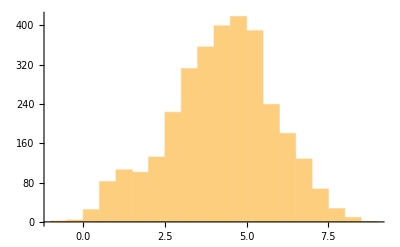

```mathematica
Histogram[ta]
```

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[23.5],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

```mathematica
{Mean[ta2],StandardDeviation[ta2],Kurtosis[ta2]}
```

{-0.0363364,0.254832,2.71419}

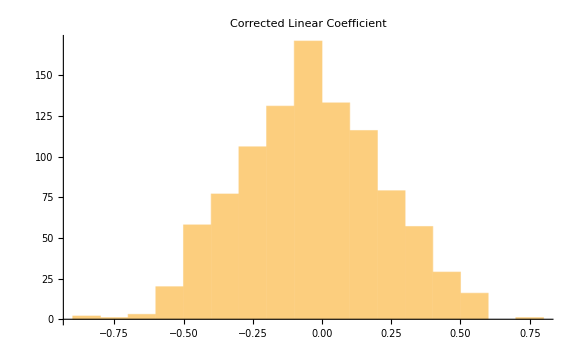

```mathematica
pl2=Histogram[ta2,PlotLabel->"Corrected Linear Coefficient",ImageSize->Large]
```

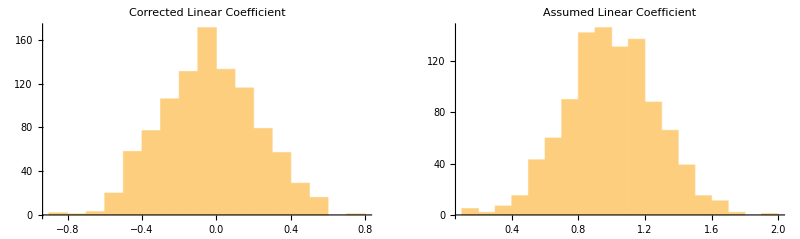

```mathematica
GraphicsGrid[{{pl2,pl1}}]
```

## Trying with low sample size.

https://twitter.com/datepsych/status/1741677937038913931 
The question is, how high is the sample count? This notebook is unfair BECAUSE I am assuming based on the sparseness of the dots, I assume each dot is one sample even though this is unlikely.
Also p-values seem to be totally useless. You run a Monte Carlo simulation, you can get any p-value you want!

-Graphics-

-Graphics-

Use the coefficients.  
What does /. mean?
It means replace values.

Note that Wolfram Engine is stringent to *

Claim is made for coefficient to be robustly is zero.

```mathematica
?/.
```

Replicate the table, how is the table replicated?

```mathematica
X=Table[i,{i,1,7,1}]
```

{1,2,3,4,5,6,7}

We do not have the total sample count. In reality, I suspect only 32 surveys were done.

```mathematica
Y={2,2,5, 8, 9, 4, 2}
```

{2,2,5,8,9,4,2}

```mathematica
ta=Table[Table[X[[i]],{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

Makes the distribution into an empirical distribution. I doubt that there are actually 32 points.

```mathematica
dist=EmpiricalDistribution[ta]
```

DataDistribution[…]

From a power law discussion, the square of a variable has half the tail exponent.

```mathematica
Histogram[ta,10,Probability,PlotLabel->"Empirical Probability Distribution of Original Data",AxesLabel->{"Amount of Muscularity (1-7)","Probability"},ImageSize->Large]
```

-Graphics-

This is the key step in replicating the paper. Take the smooth kernel distribution. It makes the distribution of the bins smoother.

```mathematica
dist2=SmoothKernelDistribution[ta];
```

Apply N to all these values which makes them real and not fractions.

```mathematica
{Mean[dist2],Kurtosis[dist2],Skewness[dist2]}//N
```

{4.25,2.8088,-0.242821}

```mathematica
{Skewness[ta],Skewness[dist2]}//N
```

{-0.319444,-0.242821}

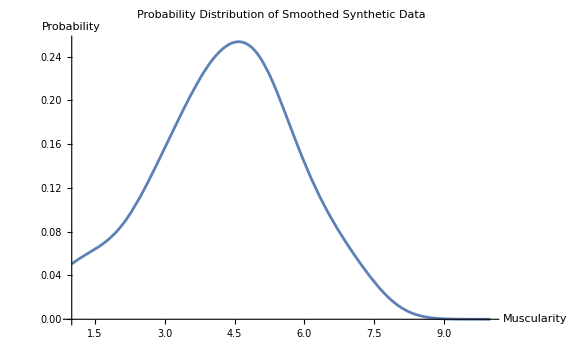

```mathematica
Plot[PDF[dist2,x],{x,1,10},PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity","Probability"},ImageSize->Large]
```

Muscularity of individuals apparently follow a normal distribution

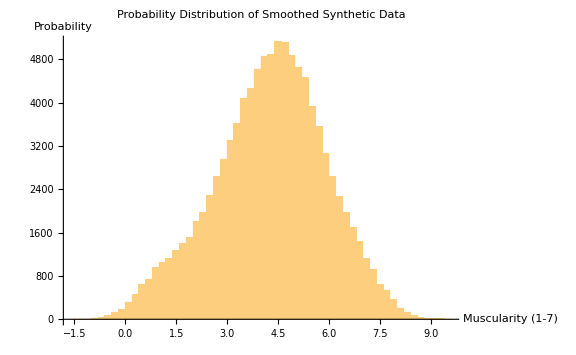

```mathematica
Histogram[RandomVariate[dist2,10^5],50,PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity (1-7)","Probability"},ImageSize->Large]
```

### Testing with No Noise

We find the gradient of a line.

```mathematica
(37-30)/7
```

1

From the picture of the graph, we derive this linear fit.

```mathematica
f=a*x+b/.{a->1,b->30};
```

Apply the regression line to the original function.

```mathematica
f1=f/.x->ta;
```

```mathematica
reg=Transpose[{ta,f1}];
```

```mathematica
lm=LinearModelFit[reg,{1,x},x];
```

Recall the table above was to get this linear regression fit of R^2=1 given the coefficients.

```mathematica
lm
```

FittedModel[30.+1. x]

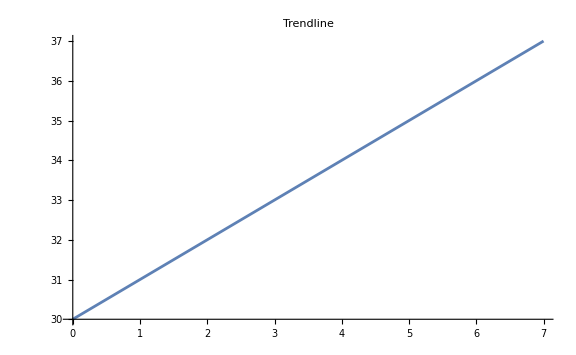

```mathematica
Plot[lm[x],{x,0,7},PlotLabel->"Trendline",ImageSize->Large]
```

Obtain the length of f1 based on the length of samples in ta.

```mathematica
f1//Length
```

32

Apply some Gaussian noise to the function. Then perform the transpose to make it suitable for regression again.

```mathematica
reg1[sigma_]:=Transpose[{ta,f1+RandomVariate[NormalDistribution[0,sigma],Length[f1]]}]
```

Then, apply a linear model fit with the model. Check the p-value as usual, run about the model 10^4 times so as to get a distribution of possible p-values. This is the Monte Carlo simulation for possible p-value given a particular noise and eats up a lot of time. I have calibrate the noise so as to get the supposed p-value.

```mathematica
res=Table[lm=LinearModelFit[reg1[2.225],{1,x},x];lm["ParameterPValues"][[2]],{z,1,10^3}];
```

Get the assumed p-value distribution and parameters.

```mathematica
{Mean[res],StandardDeviation[res],Skewness[res],Kurtosis[res]}
```

{0.0080204,0.0260059,7.13411,74.179}

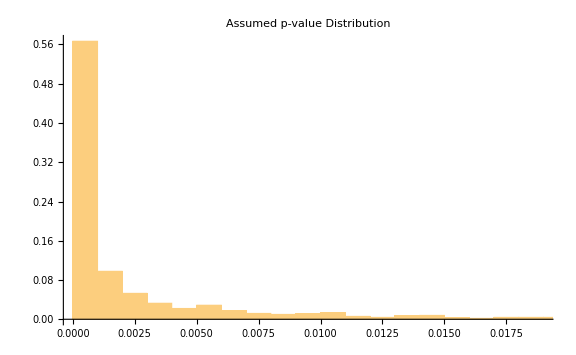

```mathematica
pl0=Histogram[res,Automatic,"Probability",PlotLabel->"Assumed p-value Distribution",ImageSize->Large]
```

Replicate the graph. From the empirical distribution. I now use 32 samples from the dots they had.

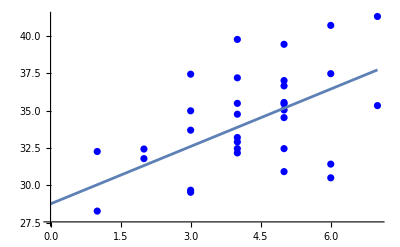

```mathematica
Show[ListPlot[reg1[2.225],PlotStyle->Blue],Plot[lm[x],{x,0,7}]]
```

### Replicating Their Linear Term

Apply the same technique, tabulate the values of the second coefficient, run the Monte Carlo simulation 10^4 times. We use purely the linear term.

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[2.225],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

Get the distribution parameters of the quadratic term.

```mathematica
{Mean[ta2],StandardDeviation[ta2],Skewness[ta2],Kurtosis[ta2]}
```

{0.991593,0.252728,-0.0293917,2.98429}

Plot the histogram of the assumed quadratic coefficient.

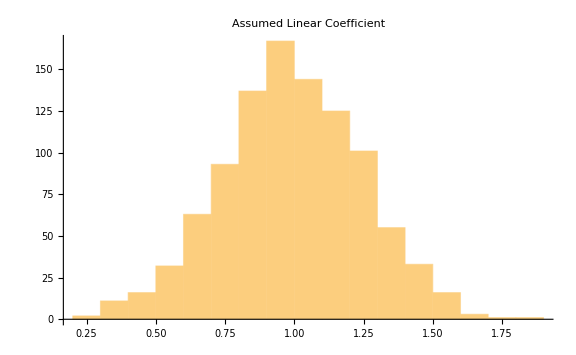

```mathematica
pl1=Histogram[ta2,PlotLabel->"Assumed Linear Coefficient",ImageSize->Large]
```

### Monte-Carlo of both the distribution and the quadratic term.

This is where you get caught out. If you have a low sample count, you should get basically nothing or no correlation. How is it possible that with such a low sample count they got such a distribution?

```mathematica
ta=RandomVariate[dist2,Length[f1]]
```

{4.10517,1.59628,4.39244,3.33011,2.49182,5.62549,6.56419,3.50217,5.65725,6.14202,0.81022,6.83803,2.72083,2.13768,4.36278,5.96483,3.11534,3.8596,4.11547,5.22445,6.91756,7.75292,5.25579,3.81053,2.37149,6.55492,5.27392,2.22651,2.50308,3.24682,3.20621,3.6746}

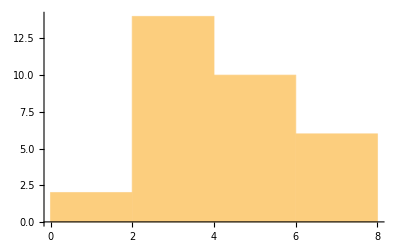

```mathematica
Histogram[ta]
```

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[2.225],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

```mathematica
{Mean[ta2],StandardDeviation[ta2],Kurtosis[ta2]}
```

{0.0292035,9.87157×10^-6,3.02676}

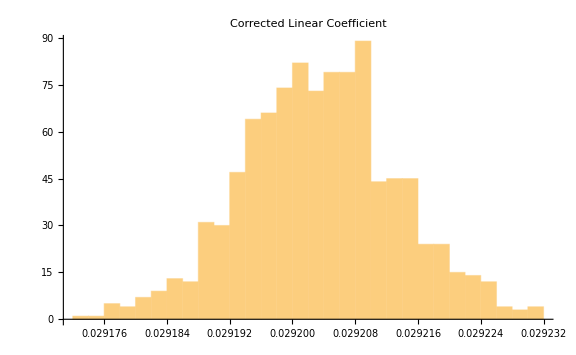

```mathematica
pl2=Histogram[ta2,PlotLabel->"Corrected Linear Coefficient",ImageSize->Large]
```

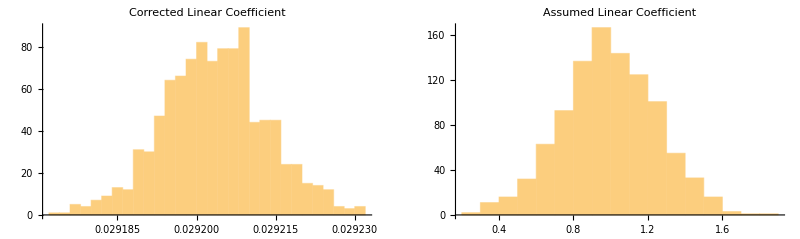

```mathematica
GraphicsGrid[{{pl2,pl1}}]
```

```mathematica
lm2["ParameterPValues"][[2]]
```

0.855268